```mathematica
{c2,d1}={1.00204463548627046268255525103062863881787524592975484988664478538400835833119`50.,1.01484601525035362520880471210616195835180782770712141707529287827317384664582`50.};
```

```mathematica
a=0.01;
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=0.01;u0=10^-10;δstart=10^-10;m=100;αSch=2m;ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=Simplify[- α/# Erf[#/(√2 a)]-2π α c2 a^2 δa[#]+(π α)/2 d1 a^4(-(3 ⅇ^(-#^2/(2 a^2)))/(2 √2 a^5 π^(3/2))+(ⅇ^(-#^2/(2 a^2)) #^2)/(2 √2 a^7 π^(3/2)))&[r]];V[r_]=-α/r;
```

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
RealEigenEnergy[n_]=-(m α^2)/(2 n^2);
Table20REE=Table[RealEigenEnergy[n],{n,20}]
```

{-0.005,-0.00125,-0.000555556,-0.0003125,-0.0002,-0.000138889,-0.000102041,-0.000078125,-0.0000617284,-0.00005,-0.0000413223,-0.0000347222,-0.0000295858,-0.0000255102,-0.0000222222,-0.0000195313,-0.000017301,-0.0000154321,-0.0000138504,-0.0000125}

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{ef,evShifted},
PrintTemporary[V];
Module[{shift=10,d=2000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
Table[
PrintTemporary[n];
Module[{sol,evnew,steps=∞,time1,time2},
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,MaxSteps->steps,opt1];
evnew=e/.
FindRoot[u[e][min]==0/.sol,If[n<5,{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[evShifted],{e,SetPrecision[0.99#[[n]],6],SetPrecision[1.01#[[n]],6]}&[Table20REE]],opt2(*,StepMonitor:>PrintTemporary[e]*)]],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All(*,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}*)(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])(*u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]*)/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
(*PrintTemporary["End with "<>ToString[time2-time1]<>"s"];*)
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
PrintTemporary[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
PrintTemporary[{estart,eend}];
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}]]
```

```mathematica
δexpminus10=δ50e[10^-10,V[r]];
δexpminus9=δ50e[10^-9,V[r]];
δexpminus5=δ50e[10^-5,V[r]];
(*δ50V=δ50[V[r]]*)
```

NDSolve::precw: 微分方程的精度 ({{200 (1/10000000000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.000678812640161460360327585430028974190240877271907) 小于 WorkingPrecision (50.).

NDSolve::precw: 微分方程的精度 ({{200 (1/1000000000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.00214659338689587061309750982064872067317767616906) 小于 WorkingPrecision (50.).

NDSolve::precw: 微分方程的精度 ({{200 (1/100000+0.01 Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::precw: 参数函数的精度 (Tan[δ]==-0.21359272401743888991655483076486271183118667502) 小于 WorkingPrecision (50.).

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{10^-15,Which[n<10,1000,11≤n<15,1800,15≤n<19,3000,n≥19,4000]},{WorkingPrecision->30,PrecisionGoal->20,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->20,MaxIterations->100}]
```

```mathematica
EigenEnergySolo[Vs2[r,a,{c2,d1}],αSch,{10^-15,2000},{-0.005,-0.006},{PrecisionGoal->15},{(*WorkingPrecision->30,*)PrecisionGoal->20,MaxIterations->100}]
```

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

ParametricNDSolve::nlnum: 在 {r$2706,u[r$2706],u'[r$2706],e$2705} = {0.,-2.32413×10^-27,3.20895×10^-30,-0.005} 处，函数值 {3.20895×10^-30,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

InterpolatingFunction::dmval: 输入值 {1/1000000000000000} 位于插值函数的数据范围之外. 将使用外推法.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

ParametricNDSolve::nlnum: 在 {r$2706,u[r$2706],u'[r$2706],e$2705} = {0.,-9.54517×10^-28,-2.49257×10^-30,-0.006} 处，函数值 {-2.49257×10^-30,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

InterpolatingFunction::dmval: 输入值 {1/1000000000000000} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0. ComplexInfinity.

General::stop: 在本次计算中，Infinity::indet 的进一步输出将被抑制.

ParametricNDSolve::nlnum: 在 {r$2706,u[r$2706],u'[r$2706],e$2705} = {0.,-9.54515×10^-28,-2.49258×10^-30,-0.006} 处，函数值 {-2.49258×10^-30,Indeterminate} 不是由数字组成的维度为 {2} 的列表.

General::stop: 在本次计算中，ParametricNDSolve::nlnum 的进一步输出将被抑制.

{-0.00648856,1.4782×10^-25}time:0.135095s

{-0.00688216,1.22538×10^-25}time:0.003009s

{-0.00710502,1.1055×10^-25}time:0.005998s

{-0.00711296,1.1015×10^-25}time:0.011009s

{-0.00929915,1.05553×10^-25}time:0.005003s

{-0.0143187,2.13156×10^-26}time:0.003002s

{-0.0155888,1.56333×10^-26}time:0.002001s

{-0.0190834,7.58568×10^-27}time:0.002002s

{-0.0223773,4.37134×10^-27}time:0.003002s

{-0.0268569,2.37809×10^-27}time:0.003002s

{-0.0322013,1.33313×10^-27}time:0.003003s

{-0.0390196,7.45276×10^-28}time:0.003002s

{-0.039884,6.98892×10^-28}time:0.003002s

{-0.0411865,6.36538×10^-28}time:0.003001s

{-0.0412696,6.32838×10^-28}time:0.005004s

{-0.041314,6.30873×10^-28}time:0.006004s

{-0.0413363,6.28501×10^-29}time:0.0080057s

{-0.0413365,3.46287×10^-30}time:0.002001s

{-0.0413366,-1.44845×10^-31}time:0.002001s

{-0.0413366,3.19957×10^-34}time:0.002001s

{-0.0413366}

```mathematica
Vs2[r,a,{c2,d1}]
```

ⅇ^(-5000. r^2) (-0.703407+1012.16 r^2)-(0.01 Erf[70.7107 r])/r

```mathematica
soltemp=Block[{r1=5000.,r2=10^-10},ParametricNDSolve[{Vs2[r,a,{c2,d1}] u[r]-1/αSch u''[r]==e u[r],u[r1]==r2,u'[r1]==-r2},u,{r,r2,r1},e,MaxSteps->Infinity]]
```

{u→ParametricFunction[<>]}

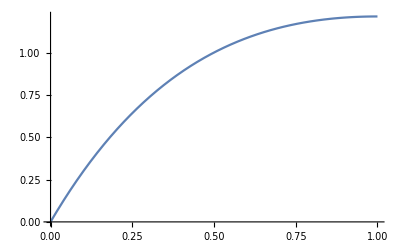

```mathematica
Plot[(u[e][r])/(u[e][0.5])/.soltemp/.e->-0.005,{r,0,1}]
```

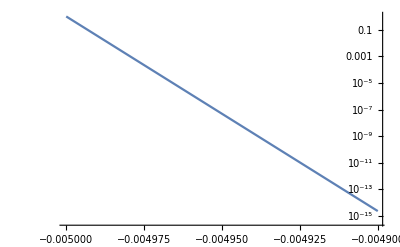

```mathematica
ListLogPlot[Table[{e,(u[e][u0])/(u[-0.005][u0])/.soltemp},{e,-0.004,-0.006,-0.0001}],Joined->True]
```

```mathematica
FindRoot[u[e][u0]==0/.soltemp,{e,-0.04,-0.06},StepMonitor:>Print[{e,u[e][u0]/.soltemp}]]
```

$Aborted